```mathematica
linked=ValueQ[linked`$Evaluatenotebook];Clear[linked`$Evaluatenotebook]
```

```mathematica
vdtdz=If[linked,linked`vdtdz,1.0]
```

#### 1. IMPORTANT: Definition of an appropriate derivative operator for the code

In this notebook, I define a derivative operator that can take care of derivatives with respect to terms enclosed in the Re[...] and Im[...] operators picking the real and imaginary parts of expressions. This operator is necessary for the current and the following notebooks, hence its placement here. Please execute this before any of the other commands in any of the notebooks.

```mathematica
deriv[expr_,var_]:=D[expr,var]//.{Re'[e_]:>Re[D[e,var]]/D[e,var],Im'[e_]:>Im[D[e,var]]/D[e,var],Arg'[e_]:>Im[D[e,var]/e]/D[e,var],Abs'[e_]:>(Re[e] Re[D[e,var]]+Im[e] Im[D[e,var]])/(Abs[e] D[e,var])}
```

#### Definition of theory parameters

The first thing is to define the numerical values of the theory parameters (Table 1, p.5).

```mathematica
higgsmass=125.3;
Hmass=56;
Hchmass=330;
Amass=330;
λ345=0.0037;
λ2=0.4;

delta1=1246.03;
delta2=1009.01;
delta3=-0.011039;


mW0=80.38;
mZ0=91.19;
WeinbergTheta=ArcCos[mW0/mZ0];
g=(2*mW0)/246.22;
gp=g*Tan[WeinbergTheta];

yt=Sqrt[2]*173/246.22;
yb=Sqrt[2]*4.18/246.22;
ytau=Sqrt[2]*1.78/246.22;
```

#### Calculation of the tree-level potential

Here, we will provide the tree-level potential. Only the CP-even part contributes dynamically (the remaining fields are assumed to be zero at the vev, hence no contribution to the tree-level potential). It is given by the following expression:

```mathematica
replaceVev={v->246.22};
replacePar={λ1->higgsmass^2/(2*v^2),λ3->λ345+2*(Hchmass^2-Hmass^2)/v^2,λ4->(Amass^2+Hmass^2-2*Hchmass^2)/v^2,λ5->(Hmass^2-Amass^2)/v^2,μ2sq->Hmass^2-(λ345*v^2)/2};
Q=v/.replaceVev;

treepotential[h1_,h2_]:=(h1^4 λ1)/4-1/2 h1^2 v^2 λ1+(h2^4 λ2)/4+1/4 h1^2 h2^2 λ3+1/4 h1^2 h2^2 λ4+1/4 h1^2 h2^2 λ5+(h2^2 μ2sq)/2;
```

#### Masses in the theory

```mathematica
masstsq[T_,h1_,h2_]:=1/2*yt^2*h1^2;
massbsq[T_,h1_,h2_]:=1/2*yb^2*h1^2;
massTausq[T_,h1_,h2_]:=1/2*ytau^2*h1^2;
massγsq[T_,h1_,h2_]:=(h1^2+h2^2)/8*(g^2+gp^2)+(g^2+gp^2)*T^2-Sqrt[((h1^2+h2^2+8*T^2)^2)/64*(g^2+gp^2)^2-g^2*gp^2*T^2*(h1^2+h2^2+4*T^2)];(*???*)
massZsq[T_,h1_,h2_]:=(h1^2+h2^2)/8*(g^2+gp^2)+(g^2+gp^2)*T^2+Sqrt[((h1^2+h2^2+8*T^2)^2)/64*(g^2+gp^2)^2-g^2*gp^2*T^2*(h1^2+h2^2+4*T^2)];(*???*)
massWsq[T_,h1_,h2_]:=(h1^2+h2^2)/v^2*mW0^2+2*g^2*T^2;
massHsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+144 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+144 h2^2 λ2+24 T^2 λ2+16 T^2 λ3+24 h1^2 λ345+24 h2^2 λ345+8 T^2 λ4+48 μ2sq-12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+24 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+24 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+24 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+144 h1^4 λ1^2+48 h1^2 T^2 λ1^2+4 T^4 λ1^2-96 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-24 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-24 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-24 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-288 h1^2 h2^2 λ1 λ2-48 h1^2 T^2 λ1 λ2-48 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+96 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+144 h2^4 λ2^2+48 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ345+4 h2^2 T^2 yb^2 λ345-4 h1^2 T^2 yt^2 λ345+4 h2^2 T^2 yt^2 λ345-4 h1^2 T^2 ytau^2 λ345+4 h2^2 T^2 ytau^2 λ345-48 h1^4 λ1 λ345+48 h1^2 h2^2 λ1 λ345-8 h1^2 T^2 λ1 λ345+8 h2^2 T^2 λ1 λ345+16 h1^2 v^2 λ1 λ345-16 h2^2 v^2 λ1 λ345+48 h1^2 h2^2 λ2 λ345-48 h2^4 λ2 λ345+8 h1^2 T^2 λ2 λ345-8 h2^2 T^2 λ2 λ345+4 h1^4 λ345^2+56 h1^2 h2^2 λ345^2+4 h2^4 λ345^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-96 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+96 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ345 μ2sq-16 h2^2 λ345 μ2sq+16 μ2sq^2)));
massHiggssq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+144 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+144 h2^2 λ2+24 T^2 λ2+16 T^2 λ3+24 h1^2 λ345+24 h2^2 λ345+8 T^2 λ4+48 μ2sq+12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+24 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+24 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+24 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+144 h1^4 λ1^2+48 h1^2 T^2 λ1^2+4 T^4 λ1^2-96 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-24 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-24 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-24 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-288 h1^2 h2^2 λ1 λ2-48 h1^2 T^2 λ1 λ2-48 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+96 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+144 h2^4 λ2^2+48 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ345+4 h2^2 T^2 yb^2 λ345-4 h1^2 T^2 yt^2 λ345+4 h2^2 T^2 yt^2 λ345-4 h1^2 T^2 ytau^2 λ345+4 h2^2 T^2 ytau^2 λ345-48 h1^4 λ1 λ345+48 h1^2 h2^2 λ1 λ345-8 h1^2 T^2 λ1 λ345+8 h2^2 T^2 λ1 λ345+16 h1^2 v^2 λ1 λ345-16 h2^2 v^2 λ1 λ345+48 h1^2 h2^2 λ2 λ345-48 h2^4 λ2 λ345+8 h1^2 T^2 λ2 λ345-8 h2^2 T^2 λ2 λ345+4 h1^4 λ345^2+56 h1^2 h2^2 λ345^2+4 h2^4 λ345^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-96 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+96 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ345 μ2sq-16 h2^2 λ345 μ2sq+16 μ2sq^2)));
massAsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+48 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+48 h2^2 λ2+24 T^2 λ2+24 h1^2 λ3+24 h2^2 λ3+16 T^2 λ3+24 h1^2 λ4+24 h2^2 λ4+8 T^2 λ4-24 h1^2 λ5-24 h2^2 λ5+48 μ2sq+12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+8 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+8 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+8 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+16 h1^4 λ1^2+16 h1^2 T^2 λ1^2+4 T^4 λ1^2-32 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-8 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-8 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-8 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-32 h1^2 h2^2 λ1 λ2-16 h1^2 T^2 λ1 λ2-16 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+32 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+16 h2^4 λ2^2+16 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ3+4 h2^2 T^2 yb^2 λ3-4 h1^2 T^2 yt^2 λ3+4 h2^2 T^2 yt^2 λ3-4 h1^2 T^2 ytau^2 λ3+4 h2^2 T^2 ytau^2 λ3-16 h1^4 λ1 λ3+16 h1^2 h2^2 λ1 λ3-8 h1^2 T^2 λ1 λ3+8 h2^2 T^2 λ1 λ3+16 h1^2 v^2 λ1 λ3-16 h2^2 v^2 λ1 λ3+16 h1^2 h2^2 λ2 λ3-16 h2^4 λ2 λ3+8 h1^2 T^2 λ2 λ3-8 h2^2 T^2 λ2 λ3+4 h1^4 λ3^2-8 h1^2 h2^2 λ3^2+4 h2^4 λ3^2-4 h1^2 T^2 yb^2 λ4+4 h2^2 T^2 yb^2 λ4-4 h1^2 T^2 yt^2 λ4+4 h2^2 T^2 yt^2 λ4-4 h1^2 T^2 ytau^2 λ4+4 h2^2 T^2 ytau^2 λ4-16 h1^4 λ1 λ4+16 h1^2 h2^2 λ1 λ4-8 h1^2 T^2 λ1 λ4+8 h2^2 T^2 λ1 λ4+16 h1^2 v^2 λ1 λ4-16 h2^2 v^2 λ1 λ4+16 h1^2 h2^2 λ2 λ4-16 h2^4 λ2 λ4+8 h1^2 T^2 λ2 λ4-8 h2^2 T^2 λ2 λ4+8 h1^4 λ3 λ4-16 h1^2 h2^2 λ3 λ4+8 h2^4 λ3 λ4+4 h1^4 λ4^2-8 h1^2 h2^2 λ4^2+4 h2^4 λ4^2+4 h1^2 T^2 yb^2 λ5-4 h2^2 T^2 yb^2 λ5+4 h1^2 T^2 yt^2 λ5-4 h2^2 T^2 yt^2 λ5+4 h1^2 T^2 ytau^2 λ5-4 h2^2 T^2 ytau^2 λ5+16 h1^4 λ1 λ5-16 h1^2 h2^2 λ1 λ5+8 h1^2 T^2 λ1 λ5-8 h2^2 T^2 λ1 λ5-16 h1^2 v^2 λ1 λ5+16 h2^2 v^2 λ1 λ5-16 h1^2 h2^2 λ2 λ5+16 h2^4 λ2 λ5-8 h1^2 T^2 λ2 λ5+8 h2^2 T^2 λ2 λ5-8 h1^4 λ3 λ5+16 h1^2 h2^2 λ3 λ5-8 h2^4 λ3 λ5-8 h1^4 λ4 λ5+16 h1^2 h2^2 λ4 λ5-8 h2^4 λ4 λ5+4 h1^4 λ5^2+56 h1^2 h2^2 λ5^2+4 h2^4 λ5^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-32 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+32 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ3 μ2sq-16 h2^2 λ3 μ2sq+16 h1^2 λ4 μ2sq-16 h2^2 λ4 μ2sq-16 h1^2 λ5 μ2sq+16 h2^2 λ5 μ2sq+16 μ2sq^2)));
masschHsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+48 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+48 h2^2 λ2+24 T^2 λ2+24 h1^2 λ3+24 h2^2 λ3+16 T^2 λ3+8 T^2 λ4+48 μ2sq+12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+8 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+8 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+8 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+16 h1^4 λ1^2+16 h1^2 T^2 λ1^2+4 T^4 λ1^2-32 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-8 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-8 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-8 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-32 h1^2 h2^2 λ1 λ2-16 h1^2 T^2 λ1 λ2-16 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+32 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+16 h2^4 λ2^2+16 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ3+4 h2^2 T^2 yb^2 λ3-4 h1^2 T^2 yt^2 λ3+4 h2^2 T^2 yt^2 λ3-4 h1^2 T^2 ytau^2 λ3+4 h2^2 T^2 ytau^2 λ3-16 h1^4 λ1 λ3+16 h1^2 h2^2 λ1 λ3-8 h1^2 T^2 λ1 λ3+8 h2^2 T^2 λ1 λ3+16 h1^2 v^2 λ1 λ3-16 h2^2 v^2 λ1 λ3+16 h1^2 h2^2 λ2 λ3-16 h2^4 λ2 λ3+8 h1^2 T^2 λ2 λ3-8 h2^2 T^2 λ2 λ3+4 h1^4 λ3^2-8 h1^2 h2^2 λ3^2+4 h2^4 λ3^2+16 h1^2 h2^2 λ4^2+32 h1^2 h2^2 λ4 λ5+16 h1^2 h2^2 λ5^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-32 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+32 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ3 μ2sq-16 h2^2 λ3 μ2sq+16 μ2sq^2)));
massϕsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+48 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+48 h2^2 λ2+24 T^2 λ2+24 h1^2 λ3+24 h2^2 λ3+16 T^2 λ3+24 h1^2 λ4+24 h2^2 λ4+8 T^2 λ4-24 h1^2 λ5-24 h2^2 λ5+48 μ2sq-12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+8 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+8 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+8 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+16 h1^4 λ1^2+16 h1^2 T^2 λ1^2+4 T^4 λ1^2-32 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-8 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-8 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-8 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-32 h1^2 h2^2 λ1 λ2-16 h1^2 T^2 λ1 λ2-16 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+32 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+16 h2^4 λ2^2+16 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ3+4 h2^2 T^2 yb^2 λ3-4 h1^2 T^2 yt^2 λ3+4 h2^2 T^2 yt^2 λ3-4 h1^2 T^2 ytau^2 λ3+4 h2^2 T^2 ytau^2 λ3-16 h1^4 λ1 λ3+16 h1^2 h2^2 λ1 λ3-8 h1^2 T^2 λ1 λ3+8 h2^2 T^2 λ1 λ3+16 h1^2 v^2 λ1 λ3-16 h2^2 v^2 λ1 λ3+16 h1^2 h2^2 λ2 λ3-16 h2^4 λ2 λ3+8 h1^2 T^2 λ2 λ3-8 h2^2 T^2 λ2 λ3+4 h1^4 λ3^2-8 h1^2 h2^2 λ3^2+4 h2^4 λ3^2-4 h1^2 T^2 yb^2 λ4+4 h2^2 T^2 yb^2 λ4-4 h1^2 T^2 yt^2 λ4+4 h2^2 T^2 yt^2 λ4-4 h1^2 T^2 ytau^2 λ4+4 h2^2 T^2 ytau^2 λ4-16 h1^4 λ1 λ4+16 h1^2 h2^2 λ1 λ4-8 h1^2 T^2 λ1 λ4+8 h2^2 T^2 λ1 λ4+16 h1^2 v^2 λ1 λ4-16 h2^2 v^2 λ1 λ4+16 h1^2 h2^2 λ2 λ4-16 h2^4 λ2 λ4+8 h1^2 T^2 λ2 λ4-8 h2^2 T^2 λ2 λ4+8 h1^4 λ3 λ4-16 h1^2 h2^2 λ3 λ4+8 h2^4 λ3 λ4+4 h1^4 λ4^2-8 h1^2 h2^2 λ4^2+4 h2^4 λ4^2+4 h1^2 T^2 yb^2 λ5-4 h2^2 T^2 yb^2 λ5+4 h1^2 T^2 yt^2 λ5-4 h2^2 T^2 yt^2 λ5+4 h1^2 T^2 ytau^2 λ5-4 h2^2 T^2 ytau^2 λ5+16 h1^4 λ1 λ5-16 h1^2 h2^2 λ1 λ5+8 h1^2 T^2 λ1 λ5-8 h2^2 T^2 λ1 λ5-16 h1^2 v^2 λ1 λ5+16 h2^2 v^2 λ1 λ5-16 h1^2 h2^2 λ2 λ5+16 h2^4 λ2 λ5-8 h1^2 T^2 λ2 λ5+8 h2^2 T^2 λ2 λ5-8 h1^4 λ3 λ5+16 h1^2 h2^2 λ3 λ5-8 h2^4 λ3 λ5-8 h1^4 λ4 λ5+16 h1^2 h2^2 λ4 λ5-8 h2^4 λ4 λ5+4 h1^4 λ5^2+56 h1^2 h2^2 λ5^2+4 h2^4 λ5^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-32 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+32 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ3 μ2sq-16 h2^2 λ3 μ2sq+16 h1^2 λ4 μ2sq-16 h2^2 λ4 μ2sq-16 h1^2 λ5 μ2sq+16 h2^2 λ5 μ2sq+16 μ2sq^2)));
masschϕsq[T_,h1_,h2_]:=(1/96 (18 g^2 T^2+6 gp^2 T^2+12 T^2 yb^2+12 T^2 yt^2+12 T^2 ytau^2+48 h1^2 λ1+24 T^2 λ1-48 v^2 λ1+48 h2^2 λ2+24 T^2 λ2+24 h1^2 λ3+24 h2^2 λ3+16 T^2 λ3+8 T^2 λ4+48 μ2sq-12 √(T^4 yb^4+2 T^4 yb^2 yt^2+T^4 yt^4+2 T^4 yb^2 ytau^2+2 T^4 yt^2 ytau^2+T^4 ytau^4+8 h1^2 T^2 yb^2 λ1+4 T^4 yb^2 λ1-8 T^2 v^2 yb^2 λ1+8 h1^2 T^2 yt^2 λ1+4 T^4 yt^2 λ1-8 T^2 v^2 yt^2 λ1+8 h1^2 T^2 ytau^2 λ1+4 T^4 ytau^2 λ1-8 T^2 v^2 ytau^2 λ1+16 h1^4 λ1^2+16 h1^2 T^2 λ1^2+4 T^4 λ1^2-32 h1^2 v^2 λ1^2-16 T^2 v^2 λ1^2+16 v^4 λ1^2-8 h2^2 T^2 yb^2 λ2-4 T^4 yb^2 λ2-8 h2^2 T^2 yt^2 λ2-4 T^4 yt^2 λ2-8 h2^2 T^2 ytau^2 λ2-4 T^4 ytau^2 λ2-32 h1^2 h2^2 λ1 λ2-16 h1^2 T^2 λ1 λ2-16 h2^2 T^2 λ1 λ2-8 T^4 λ1 λ2+32 h2^2 v^2 λ1 λ2+16 T^2 v^2 λ1 λ2+16 h2^4 λ2^2+16 h2^2 T^2 λ2^2+4 T^4 λ2^2-4 h1^2 T^2 yb^2 λ3+4 h2^2 T^2 yb^2 λ3-4 h1^2 T^2 yt^2 λ3+4 h2^2 T^2 yt^2 λ3-4 h1^2 T^2 ytau^2 λ3+4 h2^2 T^2 ytau^2 λ3-16 h1^4 λ1 λ3+16 h1^2 h2^2 λ1 λ3-8 h1^2 T^2 λ1 λ3+8 h2^2 T^2 λ1 λ3+16 h1^2 v^2 λ1 λ3-16 h2^2 v^2 λ1 λ3+16 h1^2 h2^2 λ2 λ3-16 h2^4 λ2 λ3+8 h1^2 T^2 λ2 λ3-8 h2^2 T^2 λ2 λ3+4 h1^4 λ3^2-8 h1^2 h2^2 λ3^2+4 h2^4 λ3^2+16 h1^2 h2^2 λ4^2+32 h1^2 h2^2 λ4 λ5+16 h1^2 h2^2 λ5^2-8 T^2 yb^2 μ2sq-8 T^2 yt^2 μ2sq-8 T^2 ytau^2 μ2sq-32 h1^2 λ1 μ2sq-16 T^2 λ1 μ2sq+32 v^2 λ1 μ2sq+32 h2^2 λ2 μ2sq+16 T^2 λ2 μ2sq+16 h1^2 λ3 μ2sq-16 h2^2 λ3 μ2sq+16 μ2sq^2)));
```

#### Calculation of the 1-loop 0-temperature corrections

```mathematica
dofs={Subscript[n, Wboson]=6,Subscript[n, Zboson]=3,Subscript[n, top]=12,Subscript[n, b]=12,Subscript[n, tau]=4,Subscript[n, Higgs]=1,Subscript[n, H]=1,Subscript[n, A]=1,Subscript[n, ϕ]=1,Subscript[n, ϕch]=2,Subscript[n, Hch]=2,Subscript[n, γ]=3};

(* This is a list with the degrees of freedom of each particle. The order is the same as in the list with the masses; this is important! *)
(*G[x_]:=Re[x^2/(64 π^2)((Log[x]-2*Log[Q])-3/2)];
Ggauge[x_]:=Re[x^2/(64 π^2)((Log[x]-2*Log[Q])-5/6)];
Gtrans[x_]:=Re[x^2/(64 π^2)((Log[x]-2*Log[Q])-1/2)];*)
G[x_]:=Re[x^2/(64 π^2)((Log[x/Q^2+N[1*10^-100]])-3/2)];
Ggauge[x_]:=Re[x^2/(64 π^2)((Log[x/Q^2+N[1*10^-100]])-5/6)];
Gtrans[x_]:=Re[x^2/(64 π^2)((Log[x/Q^2+N[1*10^-100]])-1/2)]
Gγ[x_]:=Re[x^2/(64 π^2)((Log[x/Q^2+N[1*10^-100]]))]



CWV[T_,h1_,h2_]:=-Subscript[n, top]*G[masstsq[0,h1,h2]](*-Subscript[n, b]*G[massbsq[T,h1,h2]]-Subscript[n, tau]*G[massTausq[T,h1,h2]]*)+(Subscript[n, Zboson]-1)*Ggauge[massZsq[0,h1,h2]]+(Subscript[n, Zboson]-2)*G[massZsq[0,h1,h2]]+(Subscript[n, Wboson]-2)*Ggauge[massWsq[0,h1,h2]]+(Subscript[n, Wboson]-4)*G[massWsq[0,h1,h2]]+Subscript[n, Higgs]*G[massHiggssq[0,h1,h2]]+Subscript[n, H]*G[massHsq[0,h1,h2]]+Subscript[n, A]*G[massAsq[0,h1,h2]]+Subscript[n, Hch]*G[masschHsq[0,h1,h2]];


CWVwithGB[T_,h1_,h2_]:=CWV[T,h1,h2]+Subscript[n, ϕ]*G[massϕsq[0,h1,h2]]+Subscript[n, ϕch]*G[masschϕsq[0,h1,h2]];








CWpotential[T_,h1_,h2_]:=(CWV[T,h1,h2]//Rationalize[#,0]&);
CWVpotentialwithGB[T_,h1_,h2_]:=(CWVwithGB[T,h1,h2]//Rationalize[#,0]&);
```

#### Counter-terms

Unlike on the paper, we will try to impose explicit counter-terms in order to obtain the correct values for the parameters. In particular, we are interested in keeping the EW minimum as the real minimum of the 1-loop effective potential.

```mathematica
(*Counterterms[h_,s_,deltaλh_,deltaλs_,deltaω_,deltaα_,deltaρ_]:=(deltaλh+deltaω+deltaρ)*h^2+(deltaω+deltaρ+deltaλs)*s^2+deltaρ*h^2*s+deltaω*h^2*s^2+deltaλh*h^4+deltaλs*s^4-deltaα*s^3;*)

Counterterms[T_,h1_,h2_]:=1/2*deltamh*h1^2+1/2*deltamH*h2^2+1/4*deltaλ1*h1^4;

(*Counterterms[h_,s_,deltaλh_,(*deltaλs_,deltaω_,deltaα_,deltaρ_,*)deltaMuHSq_,deltaMuSSq_]:=-1/2*deltaMuHSq*h^2+1/4*deltaλh*h^4-1/2*deltaMuSSq*s^2;*)


dParams={deltamh->delta1,deltamH->delta2,deltaλ1->delta3};
```

#### 2. Calculation of the 1-loop thermal (non-0-temperature) corrections

In this section we calculate the full 1-loop thermal contributions to the effective potential. We include the photon (with 3 degrees of freedom): the x->0 limit of the full J-function J_b(x) as defined via the integral converges to(-π^4/45). The inclusion of this constant offset contribution by the photon is done by hand. Since no field dependence is present in the photon term, the dynamics of the phase transition should remain unaffected by this addition. However, it should have an effect - even if only marginal - on the degeneracy condition defining the critical temperature and the corresponding vevs.

```mathematica
JB[y_,n_]:=Re[-Sum[1 /l^2  (y) BesselK[2,Sqrt[y]l],{l,1,n}]];
JF[y_,n_]:=Re[Sum[(-1)^l /l^2  (y) BesselK[2,Sqrt[y]l],{l,1,n}]];

(* Have included the transverse modes of the photon! *)



Thermal1loopV[T_,h1_,h2_]:=(T)^4/(2*π^2)*(-Subscript[n, top]*JF[masstsq[T,h1,h2]/T^2,5](*-Subscript[n, b]*JF[massbsq[T,h1,h2]/T^2,5]-Subscript[n, tau]*JF[massTausq[T,h1,h2]/T^2,5]*)+(Subscript[n, Wboson]-4)*JB[1/T^2 massWsq[T,h1,h2],5]+(Subscript[n, Wboson]-2)*JB[1/T^2 massWsq[0,h1,h2],5]+(Subscript[n, Zboson]-2)*JB[1/T^2 massZsq[T,h1,h2],5]+(Subscript[n, Zboson]-1)*JB[1/T^2 massZsq[0,h1,h2],5]+(Subscript[n, γ]-1)*(-π^4/45)+(Subscript[n, γ]-2)*JB[1/T^2 massγsq[T,h1,h2],5]+Subscript[n, Higgs]*JB[1/T^2 massHiggssq[T,h1,h2],5]+Subscript[n, H]*JB[1/T^2 massHsq[T,h1,h2],5]+Subscript[n, ϕ]*JB[1/T^2 massϕsq[T,h1,h2],5]+Subscript[n, A]*JB[1/T^2 massAsq[T,h1,h2],5]+Subscript[n, ϕch]*JB[1/T^2 masschϕsq[T,h1,h2],5]+Subscript[n, Hch]*JB[1/T^2 masschHsq[T,h1,h2],5]);

Thermal1looppotential[T_,h_,s_]:=(Thermal1loopV[T,h,s]//Rationalize[#,0]&)
```

#### 3. Calculation of the ring contributions

```mathematica
potential0T[T_,h1_,h2_]:=(treepotential[b,c]+CWVpotentialwithGB[a,b,c]+Counterterms[a,b,c])/.{a->T,b->h1,c->h2};
H1derivativepotential0T[T_,h1_,h2_]:=deriv[potential0T[a,b,c],b]/.{a->T,b->h1,c->h2};
H2derivativepotential0T[T_,h1_,h2_]:=deriv[potential0T[a,b,c],c]/.{a->T,b->h1,c->h2};
(* T now does something, so these functions are not really useful anymore. *)



potential[T_,h1_,h2_]:=(treepotential[b,c]+CWVpotentialwithGB[a,b,c]+Counterterms[a,b,c]+Thermal1looppotential[a,b,c])/.{a->T,b->h1,c->h2};
H1derivativepotential[T_,h1_,h2_]:=deriv[potential[a,b,c],b]/.{a->T,b->h1,c->h2};
H2derivativepotential[T_,h1_,h2_]:=deriv[potential[a,b,c],c]/.{a->T,b->h1,c->h2};
```

```mathematica
(*V=treepotential[0.9*v,x]/.Params
W=(potential0T[100,0.9*v,x])/.Params/.dParams
Hder=Hderivativepotential[100,0.9*v,x]/.Params/.dParams
Sder=Sderivativepotential[100,0.9*v,x]/.Params/.dParams*)
```

```mathematica
Print["Iteration ",linked`vdtdz];
Print["MuHSq is ",muH];
Print["MuSSq is ",muS];
Print["Singlet vev is ",singletvev];
Print["Singlet mass is ",singletmass];
Print["Nucleation temperature is ",tnuclist[[linked`vdtdz]]];
(*Print["Vtree is ",V];
Print["V is ",W];
Print["Hder is ",Hder];
Print["Sder is ",Sder];*)
Print["**********"];
Print["**********"];
```

## Relaxation method for the inert doublet model

## Description

This is a general-purpose notebook featuring an algorithm able to solve coupled, second-order, strongly non-linear differential equations with either Dirichlet, Neumann or mixed conditions***. The implementation below is set to compute the solutions to the bounce equations for the singlet model discussed by A. Ahriche in  his paper “What is the criterion for a strong first order electroweak phase transition in singlet models?” (2007). The tree-level potential and all relevant corrections up to first order in perturbation theory, as well as their derivatives, are defined on separate notebooks which should ideally be executed in order before this one.

This code presents two different parametrizations of the independent variable. In order to use one, please un-comment the other.  The linear parametrization is set by default.

This work was created off an instance of the code by Manuel Bichsel (ETH Zurich) and consequently corrected, completed, upgraded and further adapted to its current use by Álvaro Lozano Onrubia (Max Planck Institute for Nuclear Physics, Heidelberg).


*** Currently, the code below operates with Neumann-type conditions. In order to switch the type of boundary condition, the user needs to adapt the code himself. Only minor changes are necessary; an outline of the algorithm can be found in chapter 16 of the book “Numerical Recipes” by Press, Flannery, Teukolsky & Vetterlin.

ATTENTION: CURRENTLY RUNNING WITH NUMERICAL METHODS AT LINEAR SOLVE - faster but could lead to numerical errors.

## Input

#### Definition of an appropriate derivative operator for the code

In this notebook, I define a derivative operator that can take care of derivatives with respect to terms enclosed in the Re[...] and Im[...] operators picking the real and imaginary parts of expressions.

```mathematica
deriv[expr_,var_]:=D[expr,var]//.{Re'[e_]:>Re[D[e,var]]/D[e,var],Im'[e_]:>Im[D[e,var]]/D[e,var],Arg'[e_]:>Im[D[e,var]/e]/D[e,var],Abs'[e_]:>(Re[e] Re[D[e,var]]+Im[e] Im[D[e,var]])/(Abs[e] D[e,var])}
```

### model settings

```mathematica
{{(* Preparations *)

Off[General::spell,General::spell1];

(* declaration of the variables, the ODEs, and the number of initial and final boundary conditions *)

(* introduction of the variable names in the same order as in the ODE equations below, but begin with time t *)
variableNames = {
"t",
"f",
"h1",
"a",
"b"
};

(* Definition of model parameters *)
(* Model parameters should ideally be defined here, before the actual equations to be solved. For users of the notebooks
calculating the effective potential: this is the spot to copy-paste the results obtained for muHSq and muSSq after executing
the whole of the first notebook. *)

(* Values in brackets correspond to the critical values *)

H1derpot0[T_,h_,s_]:=H1derivativepotential0T[T,h,s]/.replacePar/.dParams/.replaceVev;
H2derpot0[T_,h_,s_]:=H2derivativepotential0T[T,h,s]/.replacePar/.dParams/.replaceVev;

H1derpot[T_,h_,s_]:=H1derivativepotential[T,h,s]/.replacePar/.dParams/.replaceVev;
H2derpot[T_,h_,s_]:=H2derivativepotential[T,h,s]/.replacePar/.dParams/.replaceVev;

(*g=CouplingG;
Subscript[y, t]=TopYukawa;
gprime=gp;
Q=ScaleQ;*)



finiteTv1=(*202.90830406*)(*nucvevs[[linked`vdtdz,1]]*)132.0;
finiteTv2=(*230.27641849*)(*nucvevs[[linked`vdtdz,2]]*)0.;
temp=(*116.49*)(*tnuclist[[linked`vdtdz]]*)123.0;
finiteTv=Sqrt[finiteTv1^2+finiteTv2^2];
(*muHSquare=muH;*)
(*muSSquare=muS;*)

fODE[f_,l_,a_,b_] := {
a,
b,
2/time^2 f(1-f)(1-2f)-finiteTv1^2/(4*finiteTv^2)*l^2*(1-f),
2/time^2 l(1-f)^2-2/time*b+1/(g^2*finiteTv1^2*(finiteTv)^2)*H1derpot[temp,finiteTv1*l+0.0000000001,finiteTv2+0.0000000001](*changed the exponent of finiteTv*)
};


(* number of conditions and equations *)
nInitial = 2; (* number of initial boundary conditions *)
nFinal = 2; (* number of final boundary conditions *)
nStatic = 0; (* number of static equations *)




initialValues = {0,0,0,0}; 
finalValues = {1,1,0,0};}, {□}}
```

{{Null^16},{□}}

```mathematica
Print["Model settings successful!"]
```

### algorithm settings

```mathematica
(* timeFunc[tau_] lets you adjust the temporal gaps between the mesh points, where 0 ≤ tau ≤ 1; to use one of the supplied time functions just uncomment it and comment the other one;
you can also create your own time function, where timeFunc[0] = 0 *)

(*1. supplied time function: linear, tParam regulates the size of the time interval [0,tParam] *)
tParam = 10;
timeFunc[tau_] := tParam * tau;
invtimeFunc[tau_]:=tau/tParam;

(* 2. supplied time function: nonlinear, tParam regulates the distribution of the mesh points over time akin to some density parameter*)

(*tParam = 10;
timeFunc[tau_] := tau / (tParam * (1-tau));
invtimeFunc[tau_]:=(tParam*tau)/(tParam*tau+1);*)


timeMax = 10;    (* time paths will be shown in the interval [0,timeMax] *)
meshPoints = 101;  (* number of mesh points *)
equilibriumPrecision = 10^-9; (* precision of the equilibrium at finalValues *)
errorCondFunc =  "mean"; (* "mean" or "max" function to control when solution is precise enough *)
solutionPrecision = 10^-9 ;  (* (relative) precision of the solution *)
iterMax = 80;  (* maximum number of iterations *)
minSolutionValue = 10^-6;  (* nonpositive values are not allowed in Jacobi matrix; they are set to minSolutionValue *)
```

```mathematica
Print["Algorithm settings successful!"];
Print["Entering computation..."];
```

## Computation

### check for user input errors

```mathematica
nTotal = nInitial+nFinal+nStatic;

relax::numberOfVariables1 =
	"Error: The total number of equations in fODE[] and fSTAT[] is not equal to the number of variables, nInitial+nFinal+nStatic.";
relax::numberOfVariables2 =
	"Error: The total number of equations in fODE[] and fSTAT[] is not equal to the number of variable names in variableNames (without time t).";If[SameQ[Head[Apply[fSTAT,initialValues]], List],  (* fSTAT[] has been defined *)
	countFunc = Length[Apply[fODE1,initialValues]] + Length[Apply[fSTAT,initialValues]],
	(* else *)
	countFunc = Length[Apply[fODE1,initialValues]]
];
If[countFunc ≠ nTotal, Message[relax::numberOfVariables1]];
If[countFunc ≠ Length[variableNames]-1, Message[relax::numberOfVariables2]];

relax::convergenceFinalValues = "Warning: finalValues does not seem to be an equilibrium point; not each value of fODE and/or fSTAT is near enough to zero, i.e. in the interval [-equilibriumPrecision, equilibriumPrecision] = [-`1`, `1`].";
If[Max[Abs[Apply[fODE1,finalValues]]]>equilibriumPrecision || Abs[Apply[fSTAT,finalValues]] > equilibriumPrecision,Message[relax::convergenceFinalValues, equilibriumPrecision]];

(* Caution: if you allow more than "mean" or "max" as keywords for constructing the relative error, do not forget to change the definition of relError at the end of the while loop in the last subsection of the computation part *)
relax::errorCondFunc = "Warning: The value \"`1`\" you used for the string variable errorCondFunc is not allowed; use \"mean\" or \"max\" instead. In this run \"max\" will be used.";
If[errorCondFunc!="mean"&&errorCondFunc!="max",
	Message[relax::"errorCondFunc",errorCondFunc];
	errorCondFunc = "max";
];
```

```mathematica
Print["Check for user input errors successful!"];
```

### computing boolean variables which reflect user input:

```mathematica
existStaticEq = If[nStatic > 0,True,False];
existFinalEq = If[ValueQ[finalEqIndex],True,False];
```

```mathematica
Print["Computing booleans successful!"];
```

### computing the derivative of the time function, and the length of a time step

```mathematica
(* construction of the derivative of the time function *)
timeFuncDerivat[tau_] := (Simplify[D[timeFunc[timeVar], timeVar]] /. timeVar->tau);
invtimeFuncDerivat[tau_]:=(Simplify[D[invtimeFunc[timeVar], timeVar]] /. timeVar->tau);

deltaTau = 1 / (meshPoints - 1);  (* remember: 0 ≤ tau ≤ 1, and the interval [0,1] will be linearly spaced with timestep deltaTau *)
```

```mathematica
Print["Computing the derivative of the time function successful!"];
Print["Entering computation of the first instances of the solution and error vectors..."];
```

### computing the first instances of the solution and error vectors solution and error, and computing the time vector timeList

```mathematica
(* solution:solution vector (var_1(t),var_2(t),...,var_n(t));will continually be updated by the algorithm
   error:error function,which should vanish by iteratively updating solution
*)

(* solution = Flatten[Table[finalValues,{meshPoints}]]; *)
solution=Flatten[Join[RandomInteger[{1,10},Length[finalValues]*(meshPoints-1)],Table[finalValues,{1}]]];
(*solution=Flatten[Join[Table[i/(Length[finalValues]*(meshPoints-1)),{i,Length[finalValues]*(meshPoints-1)}],Table[finalValues,{1}]]];*)
errorFinal := If[existFinalEq,
	Apply[fODE,solution[[Range[(meshPoints-1)*nTotal+1,meshPoints*nTotal]]]][[finalEqIndex]],
	(* else *)
(*solution[[Range[(meshPoints-1)*nTotal+nInitial+1,(meshPoints-1)*nTotal+nInitial+nFinal]]]-finalValues[[Range[nInitial+1,nInitial+nFinal]]]*)
solution[[Range[(meshPoints-1)*nTotal+1,(meshPoints-1)*nTotal+nFinal]]]-finalValues[[Range[1,nFinal]]]
 ]
error = If[existStaticEq,
Flatten[{solution[[Range[nInitial]]]-initialValues[[Range[nInitial]]],Apply[fSTAT,solution[[Range[nTotal]]]],Table[{Table[solution[[nTotal*i+j]]-solution[[nTotal*i-nTotal+j]],{j,1,nTotal-nStatic}]-deltaTau*Apply[fODE,Table[(solution[[nTotal*i+j]]+solution[[nTotal*i-nTotal+j]])/2,{j,1,nTotal}]] *  timeFuncDerivat[((i-1)*deltaTau + i*deltaTau)/2],Apply[fSTAT,Table[solution[[nTotal*i+j]],{j,1,nTotal}]]},{i,1,meshPoints-1}],errorFinal}],
(* else *)
Flatten[{solution[[Range[nInitial]]]-initialValues[[Range[nInitial]]],Table[{Table[solution[[nTotal*i+j]]-solution[[nTotal*i-nTotal+j]],{j,1,nTotal-nStatic}]-deltaTau*Apply[fODE,Table[(solution[[nTotal*i+j]]+solution[[nTotal*i-nTotal+j]])/2,{j,1,nTotal}]] *  1/invtimeFuncDerivat[time]}/.time->timeFunc[((i-1)*deltaTau + i*deltaTau)/2],{i,1,meshPoints-1}],errorFinal}]
];

tauListReduced = Range[0,1-deltaTau,deltaTau];
(* timeFunc[1] may not be a real number -> insert Infinity *)
Off[Power::infy]; 
timeList = N[Append[Map[timeFunc,tauListReduced], If[NumberQ[timeFunc[1]],timeFunc[1],Infinity]]];
On[Power::infy];
```

```mathematica
Print["Successful calculation of the first solution and error vectors!"];
Print["Entering the relaxation stage..."];
(*Print["Solution: ",solution];*)
(*Print["Error: ",error];*)
```

### The Jacobian matrix jac is constructed, so that jac(solution) * deltaSolution = -error(solution) can be solved for deltaSolution and deltaSolution added to solution. This will be iterated until the relative error, i.e. error/solution, is smaller than solutionPrecision or the maximum number of iterations, iterMax, has been reached. Then the solution matrix with (time, var_1, var_2, ..., var_n) is constructed.

```mathematica
tComputation = Timing[

(* Jacobi matrix jac consists of blocks jacLeft and jacRight which are first constructed in symbolic form, to be filled in later with real values. The last rows of jac depend on whether final conditions are given directly by concrete values in finalValues or indirectly by ODEs which have to be fullfilled at the end, designated by finalEqIndex *)

upper = Table[xUpper[i], {i,nTotal}];
lower = Table[xLower[i], {i,nTotal}];

Print["About to create bulk of symbolical Jacobian..."];

If[existStaticEq,jacLeft = D[Flatten[{upper[[Range[nInitial+nFinal]]]-lower[[Range[nInitial+nFinal]]]-deltaTau*Apply[fODE,(upper+lower)/2]*timeFuncDerivat[tau],Apply[fSTAT,upper]}],{lower}];
jacRight = D[Flatten[{upper[[Range[nInitial+nFinal]]]-lower[[Range[nInitial+nFinal]]]-deltaTau*Apply[fODE,(upper+lower)/2]*timeFuncDerivat[tau],Apply[fSTAT,upper]}],{upper}];,
(* else *)
jacLeft = 
Transpose[Table[deriv[Flatten[{upper[[Range[nInitial+nFinal]]]-lower[[Range[nInitial+nFinal]]]-deltaTau*Apply[fODE,(upper+lower)/2]*1/invtimeFuncDerivat[time]}],lower[[i]]],{i,1,nInitial+nFinal}]];
jacRight = 
Transpose[Table[deriv[Flatten[{upper[[Range[nInitial+nFinal]]]-lower[[Range[nInitial+nFinal]]]-deltaTau*Apply[fODE,(upper+lower)/2]*1/invtimeFuncDerivat[time]}],upper[[i]]],{i,1,nInitial+nFinal}]]
];

Print["Done creating bulk of symbolical Jacobian..."];
Print["About to create jacFinal..."];

jacFinal = If[existFinalEq,
{Flatten[Table[{nInitial+nStatic+(meshPoints-1)*nTotal+j,(meshPoints-1)*nTotal+k}, {j,nFinal}, {k,nTotal}],1],
Flatten[(D[Apply[fODE,lower], {lower}] /. MapThread[RuleDelayed,{lower,solution[[Range[(meshPoints-1)*nTotal+1,meshPoints*nTotal]]]}])[[finalEqIndex]]]},
(* else *)
			(*{Table[{nInitial+nStatic+(meshPoints-1)*nTotal+j,(meshPoints-1)*nTotal+nInitial+j}, {j,1,nFinal}],Table[1, {nFinal}]}*)
{Table[{nInitial+nStatic+(meshPoints-1)*nTotal+j,(meshPoints-1)*nTotal+j}, {j,1,nFinal}],Table[1, {nFinal}]}
];

Print["Done creating jacFinal..."];

relError = solutionPrecision + 1;  (* relError must initially be greater than solutionPrecision because of head of while loop below *)
meanRelErrorList = maxRelErrorList = {};  (* used for bookkeeping *)
iterCount = 1;

(*Print[MatrixForm[jacLeft]];
Print[MatrixForm[jacRight]];

Print["jacFinal: ", jacFinal];*)

(* In the following while-loop the Jacobi matrix jac is constructed as a Mathematica sparse array. The positions of the nonzero matrix values are stored in the list jacPosition, the values themselves are stored in the list jacValue, constructed by using the symbolic block matrices jacLeft, jacRight and the symbolic final matrix jacFinal. During the process of adding matrix blocks the lists jacPosition and jacValue get deeply nested, only to be flattened in the end, just before constructing the sparse array; this looks ugly but is more efficient than flattening the lists every time after appending another block.
After the sparse matrix jac has been constructed, the equation jac(solution)*deltaSolution = -error(solution) is solved for deltaSolution, then deltaSolution is added to solution, the new error function error(solution) is computed, and *)
olderr=1;
Print["The initial error is set to ", olderr," by default."];
While[relError>solutionPrecision &&iterCount<iterMax+1,
Print["*************************************************"];
Print["Starting iteration number ",iterCount];

(* Jacobi matrix jac will be constructed in groups of n rows *)
jacPosition = {
Table[{i,i}, {i,nInitial}], Table[{i,j}, {i,nInitial+1,nInitial+nStatic}, {j,nTotal}]
};
jacValue =If[existStaticEq,
{Table[1, {nInitial}], D[Apply[fSTAT,lower],{lower}]/.Flatten[{Thread[lower->solution[[Range[nTotal]]]]}]},
Table[1, {nInitial}]
];

Print["Filling in the main blocks of the Jacobian..."];

For[i=1,i<meshPoints,i++,
jacPosition ={
jacPosition, Table[{j,k}, {j,nInitial+nStatic+(i-1)*nTotal+1,nInitial+nStatic+i*nTotal}, {k,(i-1)*nTotal+1,i*nTotal}]
};
jacValue = {
jacValue, jacLeft/.Flatten[{Thread[lower->solution[[Range[nTotal*i-(nTotal-1),nTotal*i]]]],Thread[upper->solution[[Range[nTotal*i+1,nTotal*i+nTotal]]]], tau->(((i-1)*deltaTau + i*deltaTau)/2),time->timeFunc[((i-1)*deltaTau + i*deltaTau)/2]}]
};

jacPosition = {
jacPosition, Table[{j,k}, {j,nInitial+nStatic+(i-1)*nTotal+1,nInitial+nStatic+i*nTotal}, {k,i*nTotal+1,(i+1)*nTotal}]
};
jacValue = {
jacValue, jacRight/.Flatten[{Thread[lower->solution[[Range[nTotal*i-(nTotal-1),nTotal*i]]]],Thread[upper->solution[[Range[nTotal*i+1,nTotal*i+nTotal]]]], tau->(((i-1)*deltaTau + i*deltaTau)/2),time->timeFunc[((i-1)*deltaTau + i*deltaTau)/2]}]
};
]; (* end of for loop *)

jacPosition = {jacPosition, jacFinal[[1]]};
jacValue = {jacValue, jacFinal[[2]]};

jac = SparseArray[Rule[
Partition[Flatten[jacPosition],2],
N[Flatten[jacValue]]]
];


Print["Successful generation of the numerical Jacobian..."];
If[AllTrue[jac,NumericQ],Print["All elements of jac are numerical."],Print["Some non-numeric element exists."]];

(* solving  jac(solution) * deltaSolution = -error(solution)  for deltaSolution *)
deltaSolution = LinearSolve[N[jac],N[-error]];
(*deltaSolution=Inverse[jac].(-error); *)(* Works faster, but can lead to large errors for ill-conditioned matrices. *)

(* updating solution and error; as nonpositive values for solution can cause problems with Jacobi matrix, they are set to minSolutionValue. *)
(*solution = MapThread[Max,{solution+deltaSolution,Table[minSolutionValue,{nTotal*meshPoints}]}];*)
err=1/(meshPoints*nTotal)*Total[Abs[deltaSolution]];

solution=solution+deltaSolution;
error = If[existStaticEq,
Flatten[{solution[[Range[nInitial]]]-initialValues[[Range[nInitial]]],Apply[fSTAT,solution[[Range[nTotal]]]],Table[{Table[solution[[nTotal*i+j]]-solution[[nTotal*i-nTotal+j]],{j,1,nTotal-nStatic}]-deltaTau*Apply[fODE,Table[(solution[[nTotal*i+j]]+solution[[nTotal*i-nTotal+j]])/2,{j,1,nTotal}]] *  timeFuncDerivat[((i-1)*deltaTau + i*deltaTau)/2],Apply[fSTAT,Table[solution[[nTotal*i+j]],{j,1,nTotal}]]},{i,1,meshPoints-1}],errorFinal}],
(* else *)
Flatten[{solution[[Range[nInitial]]]-initialValues[[Range[nInitial]]],Table[{Table[solution[[nTotal*i+j]]-solution[[nTotal*i-nTotal+j]],{j,1,nTotal-nStatic}]-deltaTau*Apply[fODE,Table[(solution[[nTotal*i+j]]+solution[[nTotal*i-nTotal+j]])/2,{j,1,nTotal}]] * 1/invtimeFuncDerivat[time] }/.time->timeFunc[((i-1)*deltaTau + i*deltaTau)/2],{i,1,meshPoints-1}],errorFinal}]
];

Print["Working... Just finished iteration ", iterCount, " with a total error of ", err,"."];
Print["For iterations number ",iterCount-1," and ",iterCount,", the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is ", err/olderr ,"."];
Print["Time elapsed: ", tComputation[[1]]];
Print["*************************************************"];
olderr=err;
relError=err;
iterCount++;
]; (* end of while loop *)

(* Construction of the solution matrix, columns ordered by(time,<<variableNames>>) *)

solution = Transpose[Prepend[Transpose[Partition[solution,nTotal]],timeList]];
solutionReduced = Select[solution, #[[1]]≤timeMax&];

(* Construction of the iteration log matrix: <iteration number> <mean rel. error> <max. rel. error> *)
iterationLogList = Transpose[{Range[iterCount-1],meanRelErrorList,maxRelErrorList}];
];
```

About to create bulk of symbolical Jacobian...

Done creating bulk of symbolical Jacobian...

About to create jacFinal...

Done creating jacFinal...

The initial error is set to 1 by default.

*************************************************

Starting iteration number 1

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 1 with a total error of 10.1759.

For iterations number 0 and 1, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 10.1759.

Part::partd: Part specification tComputation⟦1⟧ is longer than depth of object.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 2

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 2 with a total error of 4.33461.

For iterations number 1 and 2, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.425969.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 3

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 3 with a total error of 1.91043.

For iterations number 2 and 3, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.440739.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 4

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 4 with a total error of 1.18794.

For iterations number 3 and 4, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.621817.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 5

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 5 with a total error of 0.817421.

For iterations number 4 and 5, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.688098.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 6

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 6 with a total error of 0.536507.

For iterations number 5 and 6, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.656341.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 7

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 7 with a total error of 0.612275.

For iterations number 6 and 7, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 1.14123.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 8

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 8 with a total error of 0.360585.

For iterations number 7 and 8, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.588927.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 9

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 9 with a total error of 0.207691.

For iterations number 8 and 9, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.575984.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 10

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 10 with a total error of 0.16099.

For iterations number 9 and 10, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.775142.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 11

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 11 with a total error of 0.0671671.

For iterations number 10 and 11, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.417211.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 12

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 12 with a total error of 0.00892517.

For iterations number 11 and 12, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.13288.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 13

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 13 with a total error of 0.000524615.

For iterations number 12 and 13, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.0587793.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 14

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 14 with a total error of 3.46629×10^-6.

For iterations number 13 and 14, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.0066073.

Time elapsed: tComputation⟦1⟧

*************************************************

*************************************************

Starting iteration number 15

Filling in the main blocks of the Jacobian...

Successful generation of the numerical Jacobian...

Some non-numeric element exists.

Working... Just finished iteration 15 with a total error of 9.1097×10^-11.

For iterations number 14 and 15, the relative error SubscriptBox[err, iterCount]/(err_(iterCount - 1)) is 0.0000262808.

Time elapsed: tComputation⟦1⟧

*************************************************

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«5»},{},{}} cannot be transposed.

## Output

### Bookkeeping information

```mathematica
Print["Computation time, without input processing and output generation: ", tComputation[[1]]]
Print["Criterium for definitve solution: ",
	errorCondFunc, " relative error < ", solutionPrecision, " = solutionPrecision"];
Print["Number of iterations needed: ",iterCount-1];
Print["iteration log (iteration number, mean relative error, maximal relative error):"]
Print[iterationLogList // TableForm]
```

### The solution in table form

```mathematica
(*Print["Solution ", variableNames, ":"];
Print[solution//TableForm]*)
```

### The graphs

### plot settings

```mathematica
(* graphs to plot; numbers have the same order as in the ODEs, with 1 = time *)
plotIndex = {{1,2},{1,3},{1,4},{1,5},{2,3}}; (* (t,f), (t,u),(t,h),(t,v), (f,h) *)
```

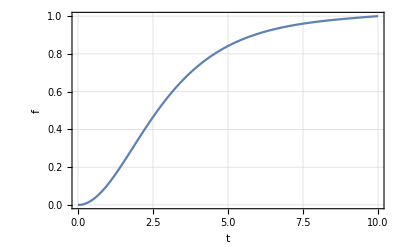

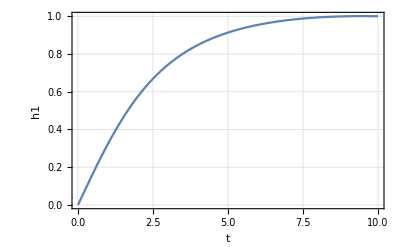

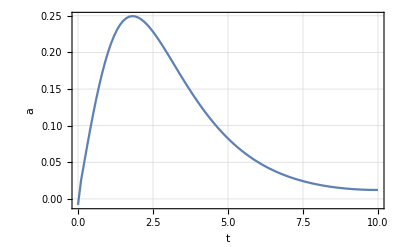

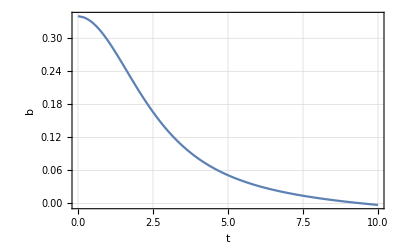

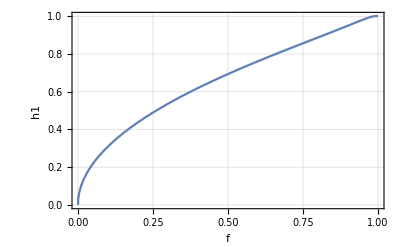

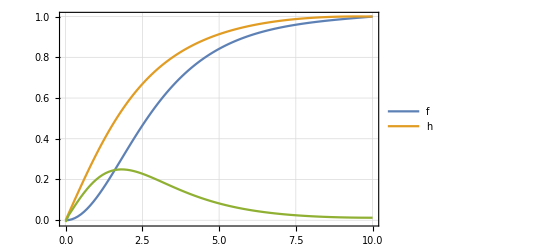

```mathematica
For[i=1,i<Length[plotIndex]+1,i++,Print[ListPlot[solutionReduced[[All,plotIndex[[i]]]],PlotRange->If[plotIndex[[i,1]]==1,{{0,timeMax},All},{All,All}],Joined->True,GridLines->Automatic,Frame->True, FrameLabel->{variableNames[[plotIndex[[i,1]]]], variableNames[[plotIndex[[i,2]]]]}]]
];
ListPlot[{solutionReduced[[All,plotIndex[[1]]]],solutionReduced[[All,plotIndex[[2]]]],solutionReduced[[All,plotIndex[[3]]]]},Joined->True,GridLines->Automatic,Frame->True,PlotRange->{{0,timeMax},All},PlotLegends->{"f","h"}]
```

### Exporting the data

```mathematica
(*dat=solution//TableForm;
Export["newsolution.dat",dat]*)
```

### Cleaning up

```mathematica
(*Clear["Global`*"];*)
```

### Analysis of the data - integration of the energy functional

First, the data is stored in a separate table, solutionshortened, which takes away the last value (since it is assigned to the radial value “Infinity”, which is non-numerical and cannot be processed). These data are then stored in solutiondata.

```mathematica
Clear[i];
```

```mathematica
solutionshortened=solution[[1;;Length[solution]-1]];
solutiondata=Table[solutionshortened[[All,i]],{i,1,5}]; (* list of lists with the mesh point values for {f,h,p,fdot,hdot,pdot}*)
```

The data are interpolated with polynomials of up to order five. It is certainly arbitrary, but it is only supposed to provide a means of comparison. The user can choose to take higher order polynomials or just use the results for any interpolation order used here.

```mathematica
Clear[i];
```

```mathematica
max⃛interpolation⃛order=1; (* HAVE DECREASED FROM 5 to 2! *)
interpolating⃛function⃛list=Table[Table[ListInterpolation[solutionshortened[[All,j]],solutionshortened[[All,1]],InterpolationOrder->i],{j,2,5}],{i,1,max⃛interpolation⃛order}]; (* list of lists of interpolating functions with splins of order j: there are max⃛interpolation⃛order lists with interpolating functions of order i arranged like {f,h,p,fdot,hdot,pdot}*)
```

The following block defines the energy functional as a function of the right-hand side limit y; i is the order of integration of the interpolation polynomials being integrated

```mathematica
Clear[i,z,y];
```

```mathematica
integralfunction[i_,z_,y_]:=NIntegrate[4*(interpolating⃛function⃛list[[i,3]][z])^2+8/z^2*(interpolating⃛function⃛list[[i,1]][z])^2*(1-interpolating⃛function⃛list[[i,1]][z])^2+z^2/2*finiteTv1^2/finiteTv^2*(interpolating⃛function⃛list[[i,4]][z])^2+finiteTv1^2/finiteTv^2*(interpolating⃛function⃛list[[i,2]][z])^2*(1-interpolating⃛function⃛list[[i,1]][z])^2+z^2/(g^2*finiteTΩ^4)*((potential[temp,finiteTv1*interpolating⃛function⃛list[[i,2]][z],finiteTv2+0.0000000001]/.replacePar/.dParams/.replaceVev)-(potential[temp,finiteTv1,finiteTv2+0.0000000001]/.replacePar/.dParams/.replaceVev)),{z,0.00001,y}];
```

```mathematica
(*integralfunction[1,z,10]*)
```

```mathematica
Clear[i];
```

```mathematica
sphaleron⃛energies=Table[integralfunction[i,z,Max[solutiondata[[1]]]],{i,1,max⃛interpolation⃛order}] (* For T=120 *)
```

```mathematica
(*Clear[solutiondata]*)
```

```mathematica
(* Do not change this! *)
(*solutiondataOld=solutiondata;*)
```

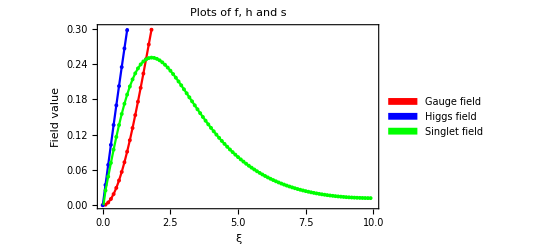

```mathematica
listplots=Show[ListPlot[Transpose@{solutiondata[[1]],solutiondata[[2]]},Joined->True,PlotRange->{{0,10},{0,Max[solutiondata[[4]]]+0.05}},PlotMarkers->{Automatic,Tiny},PlotStyle->Red,PlotLegends->SwatchLegend[{"Gauge field"},LegendMarkerSize->10,LegendMarkers->"Bubble"],Frame->True, FrameLabel->{"ξ", "Field value"},PlotLabel->"Plots of f, h and s"],ListPlot[Transpose@{solutiondata[[1]],solutiondata[[3]]},Joined->True,PlotRange->{{0,10},{0,Max[solutiondata[[4]]]+0.05}},PlotMarkers->{Automatic,Tiny},PlotStyle->Blue,PlotLegends->SwatchLegend[{"Higgs field"},LegendMarkerSize->10,LegendMarkers->"Bubble"]],ListPlot[Transpose@{solutiondata[[1]],solutiondata[[4]]},Joined->True,PlotRange->{{0,10},{0,Max[solutiondata[[4]]]+0.05}},PlotMarkers->{Automatic,Tiny},PlotStyle->Green,PlotLegends->SwatchLegend[{"Singlet field"},LegendMarkerSize->10,LegendMarkers->"Bubble"]]]
(*Show[ListPlot[Transpose@{solutiondata[[1]],solutiondata[[2]]},Joined->True,PlotRange->{{0,10},All},PlotMarkers->{Automatic,Tiny},PlotStyle->Red,PlotLegends->SwatchLegend[{"Gauge field, 0 GeV"},LegendMarkerSize->10,LegendMarkers->"Bubble"],Frame->True, FrameLabel->{"ξ", "Field value"},PlotLabel->"Comparison of the three fields at 0 GeV and 120.21 GeV"],ListPlot[Transpose@{solutiondataOld[[1]],solutiondataOld[[2]]},Joined->True,PlotRange->{{0,10},All},PlotMarkers->{Automatic,Tiny},PlotStyle->Orange,PlotLegends->SwatchLegend[{"Gauge field, 120.21 GeV"},LegendMarkerSize->10,LegendMarkers->"Bubble"](*{"Orange: Gauge field, finite T"}*)],
ListPlot[Transpose@{solutiondata[[1]],solutiondata[[3]]},Joined->True,PlotRange->{{0,10},All},PlotMarkers->{Automatic,Tiny},PlotStyle->Blue,PlotLegends->SwatchLegend[{"Higgs field, 0 GeV"},LegendMarkerSize->10,LegendMarkers->"Bubble"]],
ListPlot[Transpose@{solutiondataOld[[1]],solutiondataOld[[3]]},Joined->True,PlotRange->{{0,10},All},PlotMarkers->{Automatic,Tiny},PlotStyle->Cyan,PlotLegends->SwatchLegend[{"Higgs field, 120.21 GeV"},LegendMarkerSize->10,LegendMarkers->"Bubble"]],ListPlot[Transpose@{solutiondata[[1]],solutiondata[[4]]},Joined->True,PlotRange->{{0,10},All},PlotMarkers->{Automatic,Tiny},PlotStyle->Green,PlotLegends->SwatchLegend[{"Singlet field, 0 GeV"},LegendMarkerSize->10,LegendMarkers->"Bubble"]],ListPlot[Transpose@{solutiondataOld[[1]],solutiondataOld[[4]]},Joined->True,PlotRange->{{0,10},All},PlotMarkers->{Automatic,Tiny},PlotStyle->Yellow,PlotLegends->SwatchLegend[{"Singlet field, 120.21 GeV"},LegendMarkerSize->10,LegendMarkers->"Bubble"]]]*)
```

```mathematica
Energies=(4*π*finiteTΩ)/g*sphaleron⃛energies;
```

```mathematica
Clear[i,z,y,η];
```

```mathematica
pfunc[i_?NumericQ,z_?NumericQ,y_?NumericQ]:=pfunc[i,z,y]=1/(3*z^3)*NIntegrate[η^2*(interpolating⃛function⃛list[[i,2]][η])^2*(1-interpolating⃛function⃛list[[i,1]][η]),{η,0.00001,z}]+NIntegrate[1/(3*η)*(interpolating⃛function⃛list[[i,2]][η])^2*(1-interpolating⃛function⃛list[[i,1]][η]),{η,z,y}]
```

```mathematica
Clear[i,χ,y];
```

```mathematica
WeinbergTheta=ArcSin[Sqrt[0.22290]];
Ecorrection[i_,χ_,y_]:=NIntegrate[χ^2*(interpolating⃛function⃛list[[i,2]][χ])^2*(1-interpolating⃛function⃛list[[i,1]][χ])*pfunc[i,χ,y],{χ,0.00001,y}]
```

```mathematica
corrections=-π/3*((g*Tan[WeinbergTheta])^2*finiteTv)/g^3*Table[Ecorrection[i,r,Max[solutiondata[[1]]]],{i,1,max⃛interpolation⃛order}]
```

```mathematica
Clear[Ecorrection] (*?????*)
```

```mathematica
If[linked,{linked`maxai=(*{V,W,Hder,Sder}*)Energies,linked`masai=corrections, linked`makay=listplots,linked`SingletM=singletmass}];Plot[{(treepotential[h,x]+CWVpotentialwithGB[h,x]+Counterterms[h,x])/.Params/.dParams,treepotential[h,x]/.Params,CWVpotentialwithGB[h,x]/.Params,Counterterms[h,x]/.dParams},{h,-500,500},Frame->True,FrameLabel->{"h [GeV]","V^(T = 0)(h,s=x) [GeV^4]"},PlotLabel->"Zero-temperature potential at s=x as a function of h"]
Plot[{(potential0T[100,h,x])/.Params/.dParams,(potential[100,h,x])/.Params/.dParams},{h,-500,500},Frame->True,FrameLabel->{"h [GeV]","V^(T = 0)(h,s=x) [GeV^4]"},PlotLabel->"Zero-temperature potential and potential at T at s=x as a function of h"]
```